```mathematica
Get["new1through5Sequential.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward10[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_20Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward20[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_30Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward30[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG];
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.01;
VG =.000101;
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

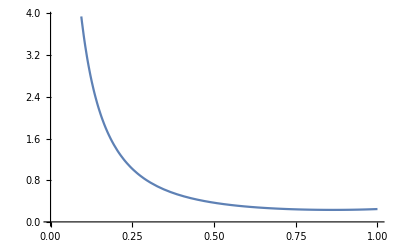

{5.01704}

{{0.0471997}}

{{0.0471997}}

0.0471997

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025]
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}]
Print[expectation]
expectation  = expectation[[1]][[1]]
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.2},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.05}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2Na10_geg10_gen50.png",%30,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2Na10_geg10_gen50.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.1}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2Na10_geg10_gen100.png",%35,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2Na10_geg10_gen100.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.15}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2Na10_geg10_gen150.png",%40,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2Na10_geg10_gen150.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.05}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2Na10_geg20_gen50.png",%45,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2Na10_geg20_gen50.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.1}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2Na10_geg20_gen100.png",%50,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2Na10_geg20_gen100.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.15}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2Na10_geg20_gen150.png",%55,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2Na10_geg20_gen150.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.05}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2Na10_geg30_gen50.png",%60,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2Na10_geg30_gen50.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.1}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2Na10_geg30_gen100.png",%65,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2Na10_geg30_gen100.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.15}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2Na10_geg30_gen150.png",%70,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2Na10_geg30_gen150.png

```mathematica
(***************************************************************************************************************************)
```

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.005;
VG =.000101;
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected,soln]
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

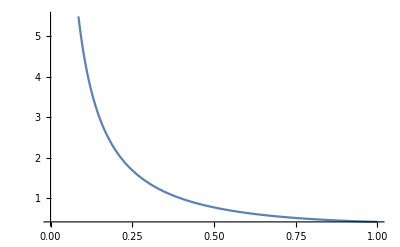

{{0.0746142}}

0.0746142

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025]
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}];
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}];
Print[expectation];
expectation  = expectation[[1]][[1]]
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,1},MaxStepSize->.00025];
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.25}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen250.png",%50,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen250.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.5}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen500.png",%55,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen500.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.75}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen750.png",%60,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen750.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.25}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg20_gen250.png",%65,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg20_gen250.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.5}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg20_gen500.png",%70,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg20_gen500.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.75}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg20_gen750.png",%75,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg20_gen750.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.25}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen250.png",%80,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen250.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.5}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen500.png",%85,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen500.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.75}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen750.png",%90,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen750.png

```mathematica
(******************************************************************************************************)
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_50Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward50[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.001;
VG =.000101;
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected,soln]
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

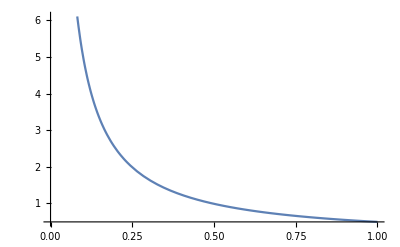

{{0.0863348}}

0.0863348

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025]
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}];
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}];
Print[expectation];
expectation  = expectation[[1]][[1]]
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.05},MaxStepSize->.00025];
```

```mathematica
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na1_geg10_gen20.png",%34,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na1_geg10_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na1_geg30_gen20.png",%38,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na1_geg30_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na1_geg50_gen20.png",%42,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na1_geg50_gen20.png

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.005;
VG =.000101;
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected,soln]
```

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025]
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}];
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}];
Print[expectation];
expectation  = expectation[[1]][[1]]
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.05},MaxStepSize->.00025];
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

-Graphics-

{{0.0746142}}

0.0746142

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen20.png",%64,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen20.png",%68,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg50_gen20.png",%72,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg50_gen20.png

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.01;
VG =.000101;
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected,soln]
```

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025]
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}];
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}];
Print[expectation];
expectation  = expectation[[1]][[1]]
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.05},MaxStepSize->.00025];
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

-Graphics-

{{0.0471997}}

0.0471997

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg10_gen20.png",%94,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg10_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg30_gen20.png",%98,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg30_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg50_gen20.png",%102,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg50_gen20.png